```mathematica
2-2
```

0

```mathematica
"\"""Resistance"" ""Distance""\""
```

Nicholas Wheeler
29 October 2011

### Introduction

A web search conducted at the end of "Master Equations" (Notebook dated 26 October 2011) led me fortuitously to a site

```mathematica
Hyperlink["Resistance Distance","http://en.wikipedia.org/wiki/Resistance_distance"]
```

which reports a pretty method for computing the resistance between any two nodes of a DC circuit. The method in question is the work of D. J. Klein [Dept. of Marine Sciences, Texas A & M] and M. Randić [Dept. of Mathematics, Drake University], published as "Resistance distance," J. of Mathematical Chemistry 12, 81 - 95 (1993). In the notebook just cited I illustrate the method—a distinguishing feature of which is that it draws upon the Moore-Penrose "psuedo-inverse"—as it pertains to a cubic array of unit resistors. I suspect—and it is my objective here to demonstrate—that it pertains also to arbitrary arrays of arbitrary resistors. 

The web site makes allusion only to arrays of unit resistors, but the Klein-Randić method would be of little interest if it worked only when all resistors in an array have unit value. The method exploits many of the ideas and graph-theoretic constructs central to my (Maxwell's!) variational method (which suffers from no such limitation), but strikes me as being much more elegantly efficient than the variational method from at least a computational point of view…even though it does not (at least in its present state of development) speak as forcefully to physical intuition as does the variational method.

My plan is to assign resistances (conductances) randomly to the edges of a complete 5-node graph

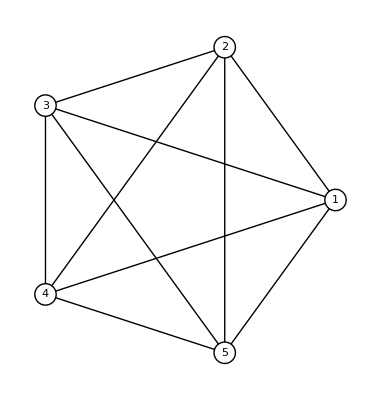

and then (1) to use the variational method to evaluate a representative sample of the

```mathematica
4+3+2+1
```

10

possible effective resistances  R_(i,j) and finally (2) to compare those results with results produced by the Klein-Randić method.

### Construction of the Laplacian matrix of a randomly weighted 5-node graph

We proceed

```mathematica
𝕒={Join[{0},Table[RandomReal[],{k,1,4}]],
Join[{0,0},Table[RandomReal[],{k,1,3}]],
Join[{0,0,0},Table[RandomReal[],{k,1,2}]],
Join[{0,0,0,0},Table[RandomReal[],{k,1,1}]],
{0,0,0,0,0}};
```

```mathematica
𝕒//MatrixForm
```

(0 | 0.0785371 | 0.166641 | 0.95681 | 0.637505
0 | 0 | 0.440486 | 0.547215 | 0.546784
0 | 0 | 0 | 0.991426 | 0.287798
0 | 0 | 0 | 0 | 0.832358
0 | 0 | 0 | 0 | 0)

```mathematica
𝕓=𝕒+Transpose[𝕒];
𝕓//MatrixForm
```

(0 | 0.0785371 | 0.166641 | 0.95681 | 0.637505
0.0785371 | 0 | 0.440486 | 0.547215 | 0.546784
0.166641 | 0.440486 | 0 | 0.991426 | 0.287798
0.95681 | 0.547215 | 0.991426 | 0 | 0.832358
0.637505 | 0.546784 | 0.287798 | 0.832358 | 0)

```mathematica
𝕕=DiagonalMatrix[Table[Total[𝕓⟦k⟧],{k,1,5}]]
𝕕//MatrixForm
```

{{1.83949,0.,0.,0.,0.},{0.,1.61302,0.,0.,0.},{0.,0.,1.88635,0.,0.},{0.,0.,0.,3.32781,0.},{0.,0.,0.,0.,2.30445}}

(1.83949 | 0. | 0. | 0. | 0.
0. | 1.61302 | 0. | 0. | 0.
0. | 0. | 1.88635 | 0. | 0.
0. | 0. | 0. | 3.32781 | 0.
0. | 0. | 0. | 0. | 2.30445)

```mathematica
𝕃=𝕓-𝕕;
𝕃//MatrixForm
```

(-1.83949 | 0.0785371 | 0.166641 | 0.95681 | 0.637505
0.0785371 | -1.61302 | 0.440486 | 0.547215 | 0.546784
0.166641 | 0.440486 | -1.88635 | 0.991426 | 0.287798
0.95681 | 0.547215 | 0.991426 | -3.32781 | 0.832358
0.637505 | 0.546784 | 0.287798 | 0.832358 | -2.30445)

and demonstrate that the symmetric matrix 𝕃 does indeed possess the properties expected/required of a Laplacian matrix:

```mathematica
Table[Total[𝕃⟦k⟧],{k,1,5}]
Eigenvalues[𝕃]
```

{0.,0.,0.,0.,0.}

{-4.2295,-2.88768,-2.13742,-1.71651,0.}

### Effective resistances by dissipation minimization

The Laplacian matrix 𝕃, as constructed above, has just been shown to be negative semi-definite, so it is the negative of the matrix we need to describe dissipation. Working therefore from

```mathematica
𝔻=-𝕃;
```

```mathematica
Eigenvalues[𝔻]
```

{4.2295,2.88768,2.13742,1.71651,0.}

the dissipation rate (net I^2 R-loss rate) is

```mathematica
Diss=Expand[Transpose[({{Subscript[V, 1]}, {Subscript[V, 2]}, {Subscript[V, 3]}, {Subscript[V, 4]}, {Subscript[V, 5]}})].𝔻.({{Subscript[V, 1]}, {Subscript[V, 2]}, {Subscript[V, 3]}, {Subscript[V, 4]}, {Subscript[V, 5]}})]⟦1⟧
```

{1.83949 V_1^2-0.157074 V_1 V_2+1.61302 V_2^2-0.333283 V_1 V_3-0.880971 V_2 V_3+1.88635 V_3^2-1.91362 V_1 V_4-1.09443 V_2 V_4-1.98285 V_3 V_4+3.32781 V_4^2-1.27501 V_1 V_5-1.09357 V_2 V_5-0.575597 V_3 V_5-1.66472 V_4 V_5+2.30445 V_5^2}

This quadratic form is to be minimized subject to constraints (Kirchhoff's nodal rule, expressed in terms of nodal potentials) that for a free circuit (one not hooked up to a current source) would read

```mathematica
FreeConstraints=Table[Sum[𝕃⟦j⟧⟦k⟧Subscript[V, k],{k,1,5}]==0,{j,1,5}]
```

{-1.83949 V_1+0.0785371 V_2+0.166641 V_3+0.95681 V_4+0.637505 V_5==0,0.0785371 V_1-1.61302 V_2+0.440486 V_3+0.547215 V_4+0.546784 V_5==0,0.166641 V_1+0.440486 V_2-1.88635 V_3+0.991426 V_4+0.287798 V_5==0,0.95681 V_1+0.547215 V_2+0.991426 V_3-3.32781 V_4+0.832358 V_5==0,0.637505 V_1+0.546784 V_2+0.287798 V_3+0.832358 V_4-2.30445 V_5==0}

but when unit current is inject at one node (node #1, let us say) and extracted at another (node #2, let us say) must be modified:

```mathematica
Subscript[C, 12]=Table[Sum[𝕃⟦j⟧⟦k⟧Subscript[V, k],{k,1,5}]==KroneckerDelta[j,2]-KroneckerDelta[j,1],{j,1,5}]
```

{-1.83949 V_1+0.0785371 V_2+0.166641 V_3+0.95681 V_4+0.637505 V_5==-1,0.0785371 V_1-1.61302 V_2+0.440486 V_3+0.547215 V_4+0.546784 V_5==1,0.166641 V_1+0.440486 V_2-1.88635 V_3+0.991426 V_4+0.287798 V_5==0,0.95681 V_1+0.547215 V_2+0.991426 V_3-3.32781 V_4+0.832358 V_5==0,0.637505 V_1+0.546784 V_2+0.287798 V_3+0.832358 V_4-2.30445 V_5==0}

The command

```mathematica
Minimize[Flatten[{Diss,Subscript[C, 12]}],{Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5]}]
```

{1.13181,{V_1→4.8507,V_2→3.71889,V_3→4.24492,V_4→4.35306,V_5→4.32675}}

now supplies

EffectiveResistance_12=1.13181

Notice that the interior nodal potentials {V_3,V_4,V_5} are bounded above by V_1 and below by V_2.

### The Klein-Randić Method

From

```mathematica
Det[𝔻]
```

0.

we see that 𝔻—equivalently 𝕃—is singular, so does not possess an inverse. It does, however, possess a Moore-Penrose pseudoinverse, which Mathematica knows how to construct:

```mathematica
?PseudoInverse
```

PseudoInverse[m] finds the pseudoinverse of a rectangular matrix.

Klein & Randić claim that if we do so

```mathematica
Γ=PseudoInverse[𝔻]
```

{{0.382865,-0.16897,-0.134966,-0.0302007,-0.0487286},{-0.16897,0.411007,-0.0810238,-0.0843987,-0.0766151},{-0.134966,-0.0810238,0.359167,-0.032826,-0.110352},{-0.0302007,-0.0843987,-0.032826,0.195926,-0.0485008},{-0.0487286,-0.0766151,-0.110352,-0.0485008,0.284196}}

REMARK: We note in passing that

```mathematica
Det[Γ]//Chop
```

0

then

```mathematica
Subscript[R, effective][i_,j_]:=Γ⟦i⟧⟦i⟧+Γ⟦j⟧⟦j⟧-2Γ⟦i⟧⟦j⟧
```

which in the present instance supplies

```mathematica
Subscript[R, effective][1,2]
```

1.13181

—in precise agreement with the result obtain above by the variational method. Similarly,

```mathematica
Subscript[R, effective][2,5]
```

0.848433

while in that case the variational method proceeds

```mathematica
Subscript[C, 25]=Table[Sum[𝕃⟦j⟧⟦k⟧Subscript[V, k],{k,1,5}]==KroneckerDelta[j,5]-KroneckerDelta[j,2],{j,1,5}];
Minimize[Flatten[{Diss,Subscript[C, 25]}],{Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5]}]
```

{0.848433,{V_1→-1.81593,V_2→-1.20807,V_3→-1.66636,V_4→-1.73159,V_5→-2.0565}}

to precisely the same result.

To obtain all possible effective resistance values one would—if using the variational method—have to repeatedly adjust the constraint equations and re-calculate. But the Klein-Randić method supplies them all at once:

```mathematica
Table[Subscript[R, effective][i,j],{i,1,5},{j,1,5}]//MatrixForm
```

(0. | 1.13181 | 1.01196 | 0.639193 | 0.764518
1.13181 | 0. | 0.932222 | 0.775731 | 0.848433
1.01196 | 0.932222 | 0. | 0.620746 | 0.864067
0.639193 | 0.775731 | 0.620746 | 0. | 0.577124
0.764518 | 0.848433 | 0.864067 | 0.577124 | 0.)

### Conclusion

Klein-Randić works when the resistances are arbitrary. But for its magical efficiency one does pay a price: the method has—in contrast to the variational method—nothing to say about the values of the nodal potentials or branch currents. It is remarkable that it manages to address intrinsic properties of the circuit—properties that the circuit possess whether or not or how the circuit is connected to a power source—without drawing upon such information.